## Population Growth

### Key

Continuous Time Model
r	 -- birth rate - death rate for continuous time model

 Discrete Time Model
 d	 -- an individual’s probability of dying
(1-d)	 -- an individuals probability of not dying

b	 -- an individual’s probability of producing a single offspring
(1-b)	 -- an individuals probability of not reproducing

### Continuous time growth

We won’t use differential equations much in this class, but right now I want to show how the continuous time an discrete time versions match up. 
Given our differential equation, we can ask Mathematica to find the solution for us:

```mathematica
D[n[t],t]==n[t]*b - n[t] * d ==n[t]*(b - d)==n[t]*r
```

```mathematica
r=b-d
```

```mathematica
DSolve[{ D[n[t],t]==r*n[t]  , n[0]==n0},n[t],t]
```

{{n[t]→ⅇ^(r t) n0}}

We can write this as a function that we can this use more generally.

```mathematica
n[r_,t_]:=n0 * Exp[r*t]
```

We can plot population size as a function of time.

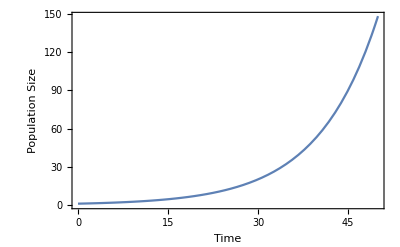

```mathematica
n0=1;continuousplot=Plot[n[0.1,t],{t,0,50} , Frame->True,FrameLabel->{"Time","Population Size"}]
```

We can also use the manipulate function in Mathematica to explore changing a parameter. The “Manipulate” command is a bit fragile, parameters to manipulate have to be passed through functions or written as formulas in the command itself. Here we allow the parameter “r” to vary between 0 and 0.1.

```mathematica
Manipulate[Plot[n[r,t],{t,0,50},PlotRange->{{0,50},{0,150}}, Frame->True,FrameLabel->{"Time","Population Size"}],{{r,0.05},-0.1,.1}]
```

We could also see what happens if r is negative:

```mathematica
Manipulate[Plot[n[t,r],{t,0,50},PlotRange->{{0,50},{0,1}}, Frame->True,FrameLabel->{"Time","Population Size"}],{{r,-0.1},-0.1,0}]
```

We can also plot on a log plot. You may have heard of these lately... Exponential growth looks linear on a log scale. Here we can vary r from -0.1 to +0.1 to see better what happens when growth is + or -. It looks really boring! On the log scale, exponential growth is just lines.

```mathematica
Manipulate[Plot[Log[n[t,r]],{t,0,50},PlotRange->{{0,50},{-4,4}}, Frame->True,FrameLabel->{"Time","Log Population Size"}],{{r,0},-.1,.1}]
```

### Discrete time growth

We’ll work with recursion equations a lot in class. It’s a little tricky to write them in a way that we can use them in Mathematica, because we often use notation when writing like n_(t+1)=f(n_t), but Mathematica won’t like that. So we define updating function,  f(n_t), and then typically use a Table or Do loop to repeatedly apply it.

Here is our recursion equation for the birth/death growth model.

```mathematica
nup[n_]:= n*(1-d)(1+b)
```

We can ask, how many mice will there be in the next generation if there are 10 now:

```mathematica
nup[10]
```

10 (1+b) (1-d)

In the lecture notes, I derived a solution to this recursion equation. This equation is now a function of time, and requires knowing the initial population size at time step 0.

```mathematica
nt[t_]:=n0 * ((1-d)(1+b))^t
```

```mathematica
R0 == (1-d)(1+b)
```

We can use it to see what the population size would be some time in the future.  Without putting in values for d and b, it just tells us what we already know, that at time t there will be R0^t more individuals.

```mathematica
Clear[n0]
```

```mathematica
Table[nt[t],{t,1,5}]
```

{(1+b) (1-d) n0,(1+b)^2 (1-d)^2 n0,(1+b)^3 (1-d)^3 n0,(1+b)^4 (1-d)^4 n0,(1+b)^5 (1-d)^5 n0}

Now we will put in values for the parameters and graph the population size.

```mathematica
n0=1;d=.1;b=0.22;
```

```mathematica
Table[ {t,nt[t]},{t,1,5}]
```

{{1,1.098},{2,1.2056},{3,1.32375},{4,1.45348},{5,1.59592}}

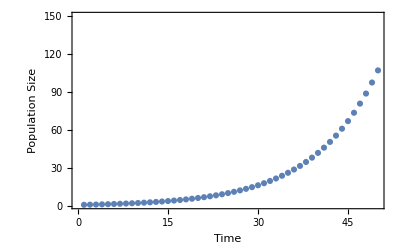

```mathematica
n0=1;d=.1;b=0.22;
discreteplot=ListPlot[Table[nt[t],{t,1,50}],PlotRange->{{0,50},{1,150}},Frame->True,FrameLabel->{"Time","Population Size"}]
```

### Comparing the two time growth

We need to choose parameters that make the models equivalent. To do this we use the formula that Log[R0] ~= r . Since there are two parameters in our R0 (i.e. R0 = (1-d)(1+b)) we just set one parameter as we choose.

Set the continuous time growth rate to 0.2

```mathematica
rcont=-0.2;
```

We’ll set the discrete time mortality rate to 0.1, and then solve for the birth rate that will produce an equivalent growth trajectory to the continuous time model.

```mathematica
Clear[b];
d=0.4;
Solve[Log[(1-d)*(1+b) ]==rcont, b]
```

{{b→0.364551}}

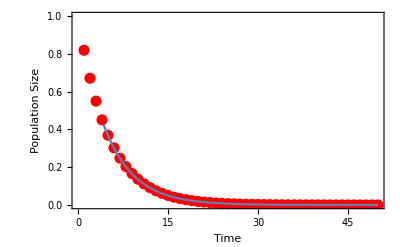

```mathematica
n0=1;d=.4;b=0.3654175733522;
discreteplot=ListPlot[Table[nt[t],{t,1,50}],PlotRange->{{0,50},{0,1}},Frame->True,FrameLabel->{"Time","Population Size"}, PlotStyle->{PointSize->.02,Red}];continuousplot=Plot[n[rcont,t],{t,0,50} , Frame->True,FrameLabel->{"Time","Population Size"}];
Show[discreteplot,continuousplot]
```

#### Try it yourself!

Now try this on your own, change r and see if you can make a discrete time model that matches it.